```mathematica
SetDirectory["/Users/sinbi/desktop/STUDY/Data_get/bb/PAMELA"];
Needs["ErrorBarPlots`"];
Get["/Users/sinbi/desktop/STUDY/Data_get/ErrorBarLogPlots.m"];
Get["/Users/sinbi/desktop/STUDY/Data_get/ProtonFluxELDRAnn.m"];
```

## PAMELA-Experiment Error Bar Import

22

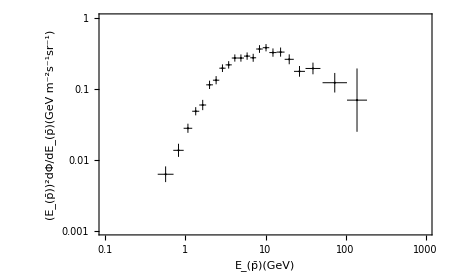

```mathematica
IErrorbp= Import["/Users/sinbi/desktop/study/Data_get/Error_data_PAMELA_Full.dat","Table",HeaderLines-> 1];
Length[IErrorbp]
IErrorbp1=Table[{IErrorbp[[i,1]],IErrorbp[[i,2]],(IErrorbp[[i,4]]-IErrorbp[[i,3]])/2,(IErrorbp[[i,6]]-IErrorbp[[i,5]])/2},{i,1,Length[IErrorbp]}];
IErrorbp2=IErrorbp1/.{x_,y_,z_,k_}->{{x,y},ErrorBar[z,k]};
ErroPlotbp=ErrorListLogLogPlot[IErrorbp2,Frame->True,Axes->False,PlotRange->{{10^-1,10^3},{10^-3,1}}, ErrorBarFunction->Automatic,ImageSize->450,PlotStyle->{Black,AbsolutePointSize[1.5],AbsoluteThickness[0.7]},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Get Background(BG)

100

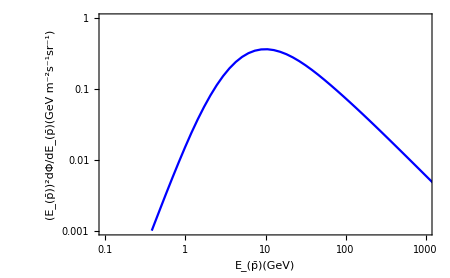

```mathematica
BGbp=Import["/Users/sinbi/desktop/study/Data_get/PAMELAMD.dat","Table","HearderLines"->1];
Length[BGbp]
ifBGbp=Interpolation[BGbp];
BGPlotbp=ListLogLogPlot[ifBGbp,Joined->True,Axes->False,Frame->True,PlotRange->{{10^-1,10^3},{10^-3,1}},ImageSize->450,PlotStyle->{Blue},FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## Dark Matter(DM)

```mathematica
primarybp="b";
halobp="Bur";
propagationbp="MAX";
mDMbp=100;
σvbp=0.7*10^-26;
Eγ=10^lEγ;
```

```mathematica
ifPobp=Interpolation[Table[{10^lEγ,10^lEγ 10.^ ProtonFluxELDRAnn[primarybp, halobp, propagationbp][mDMbp, σvbp,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}]];
```

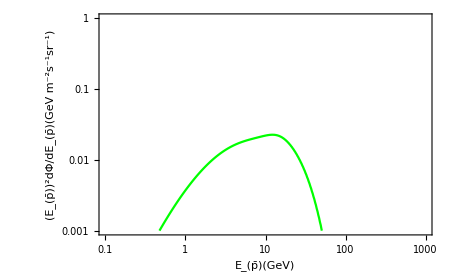

```mathematica
PlotMEDbp=ListLogLogPlot[ifPobp,PlotRange->{{10^-1,10^3},{10^-3,1}},Joined->True,PlotStyle->Green,Frame->True,Axes->False,ImageSize->450,FrameTicks-> Automatic, FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

## SUM=BG+DM

InterpolatingFunction[…]

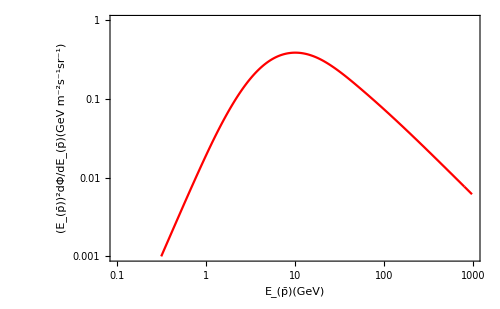

```mathematica
Sumdatabp=Interpolation[Table[{x,ifBGbp[x]+ifPobp[x]},{x,0.18,10^2.99,0.1}]]
SumPlotbp=ListLogLogPlot[Sumdatabp,Joined->True,PlotRange->{{10^-1,10^3},{10^-3,1}},PlotStyle->Red,Frame->True,Axes->False,ImageSize->500 ,FrameLabel->{"E_(p̄)(GeV)","(E_(p̄))^2dΦ/dE_(p̄)(GeV m^-2s^-1sr^-1)"}]
```

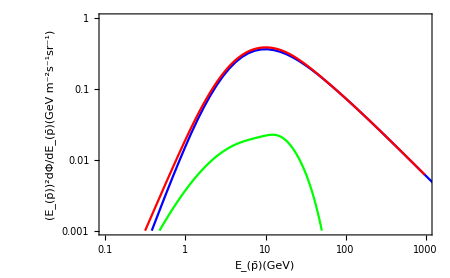

```mathematica
Show[BGPlotbp,PlotMEDbp,SumPlotbp]
```

## χ^2- Fitting

```mathematica
SumYbp=Table[Sumdatabp[IErrorbp1[[i,1]]],{i,Length[IErrorbp]}];
IErrorYbp=Flatten[Table[{IErrorbp1[[i,2]]},{i,1,Length[IErrorbp]}],1];
IErrorSizebp=Flatten[Table[{IErrorbp1[[i,4]]},{i,1,Length[IErrorbp]}],1];chiSUMbp=((SumYbp-IErrorYbp)/IErrorSizebp)^2;
Sum1=Sum[chiSUMbp[[i]],{i,1,Length[IErrorbp]}]
Re[Sum1]
```

29.9492

29.9492

## Mass-σv graph

```mathematica
ClearAll[σv02]
```

```mathematica
mDM02=10^lmDM02;
```

```mathematica
σv02=10^lσv02;
```

```mathematica
ifPobp2=Interpolation[Table[{10^lEγ,10^lEγ 10.^ ProtonFluxELDRAnn[primarybp, halobp, propagationbp][mDM02, σv02,Log[10,10^lEγ]]},{lEγ,-1,3,0.01}]];
```

```mathematica
Sumdatabp2=Interpolation[Table[{x,ifBGbp[x]+ifPobp2[x]},{x,0.18,10^2.99,0.1}]];
SumYbp2=Table[Sumdatabp2[IErrorbp1[[i,1]]],{i,Length[IErrorbp]}];
chiSUMbp2=((SumYbp2-IErrorYbp)/IErrorSizebp)^2;
FinalSumbp=Sum[chiSUMbp2[[i]],{i,1,Length[IErrorbp]}];
```

```mathematica
contbp=Flatten[Table[Re[{mDM02,lσv02,σv02,FinalSumbp}],{lmDM02,0.7,2.4,0.02},{lσv02,-28,-25,0.05}], 1];
Export["PAbb_BUR_MAX.dat",contbp,"Table"];
```

```mathematica
contablebp=Import["/Users/sinbi/desktop/study/Data_get/bb/PAMELA/PAbb_BUR_MAX.dat","Table",HeaderLines->1]
```

{{5.01187,-27.95,1.12202×10^-28,42.394},{5.01187,-27.9,1.25893×10^-28,42.3678},5241,{251.189,-25.05,8.91251×10^-26,75.1397},{251.189,-25.,1.×10^-25,89.238}}
 |  |  |  |

```mathematica
contbpLog=Table[{contablebp[[i,1]],contablebp[[i,2]], contablebp[[i, 4]]},{i, Length[contablebp]}];
```

```mathematica
Export["PAbb_table_BUR_MAX.dat",contbpLog,"Table"]
```

PAbb_table_BUR_MAX.dat

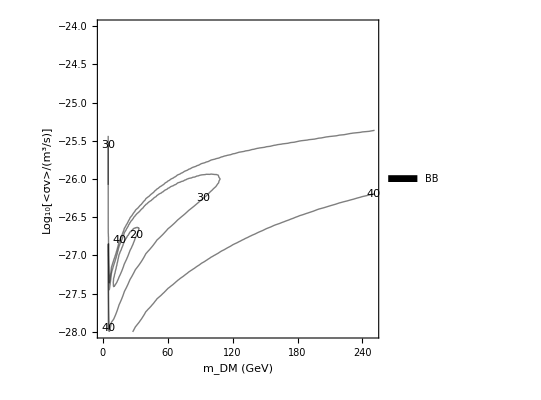

```mathematica
ListContourPlot[contbpLog,Contours-> {10,20,30,40},
FrameLabel->{"m_DM (GeV)","Log_10[<σv>/(m^3/s)]"},PlotRange->{{0,250},{-28,-24}},  ContourLabels->All,ContourShading->None,
PlotLegends->Placed[SwatchLegend[{"BB"},LegendMarkerSize->20],Right]]
```